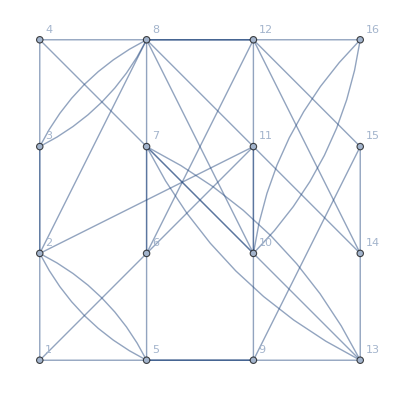
```mathematica
g=-Graphics-;
basisVectors={{0.824942872564313,0.21842747167154472},{0.7726850338214735,0.2627389437815274},{0.38296222200922175,0.8923298892003046},{0.6265355438713063,0.4909949307316633},{1.019269014436307,-0.21252327831065929},{0.31478435493119317,0.8012461230670399},{0.725752689407469,-0.3175338649785955},{0.0479657726172807,1.271845586448928},{0.9414805719375502,-0.2129482325340342},{0.5253186605473394,0.8795991887283106},{0.922373575517376,0.06102973531685047},{0.3535906890163147,0.41577563665363865},{1.655729494964778,-0.9724832046352357},{0.31478435493119317,0.8012461230670402},{0.7713245770034145,-0.8335978818453875},{0.6633076709703752,1.4729574934685317}};
(*{grounds,basisVectors} = FingerprintVectors[g,2, GroundingRandom];
basisVectors = Re[basisVectors];*)
```

{{0.824943,0.218427},{0.772685,0.262739},{0.382962,0.89233},{0.626536,0.490995},{1.01927,-0.212523},{0.314784,0.801246},{0.725753,-0.317534},{0.0479658,1.27185},{0.941481,-0.212948},{0.525319,0.879599},{0.922374,0.0610297},{0.353591,0.415776},{1.65573,-0.972483},{0.314784,0.801246},{0.771325,-0.833598},{0.663308,1.47296}}

#### Melo

```mathematica
meloV=VectorPartition[basisVectors, V[g],OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
Norm[Total[basisVectors*meloV]]
N[CriterionPartitionFunction[g,meloV,0.5]]
```

{0,1,1,1,1,1,0,1,0,1,0,1,1,1,0,1}

9.48769

41.8909

#### MeloProbe

```mathematica
meloProbeV=VectorPartition[basisVectors, V[g], Method->MeloProbe,OptimizationOn->True,OptimizationObj->(CriterionPartitionFunction[g,#,0.5]&)]
Norm[Total[basisVectors*meloProbeV]]
N[CriterionPartitionFunction[g,meloProbeV,0.5]]
```

{16,10,13,8,6,14,4,3,2,12,5,1,15,7,11,9}

{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1}

2.65912

36.5714

```mathematica
meloProbe2V=VectorMaxOnDirection[basisVectors, V[g]/2, Normalize[Total[basisVectors*meloProbeV]](*+RandomReal[{0,1},3]*)]
Norm[Total[basisVectors*meloProbe2V]]
N[CriterionPartitionFunction[g,meloProbe2V,0.5]]
```

{16,10,8,3,6,14,4,2,12,1,11,13,5,15,7,9}

{0,1,1,1,0,1,0,1,0,1,0,0,0,1,0,1}

7.64707

36.

```mathematica
basisVectors
```

{{0.475185,0.865223},{0.674399,0.14488},{0.807973,0.408165},{0.824622,0.10252},{0.536001,-0.17065},{0.827445,0.11256},{0.361969,-0.546695},{0.915153,0.195494},{0.057361,1.41982},{1.05973,0.133053},{0.441792,0.799402},{0.621307,0.0613409},{0.793446,-1.98442},{0.827445,0.11256},{0.397636,-0.133743},{1.57652,0.214942}}